Найти кривую (theta, phi) направлений синхронизма для ГВГ в LBO от 1064 нм

```mathematica
Clear["Global`*"];
```

```mathematica
Nx[λ_,T_]:=1×1×1.064/λ+0×Sqrt[2.4542+0.01125/(λ^2−0.01135)-0.01388 λ^2]-(3.76λ-2.3)×10^-6(T-293);
Ny[λ_,T_]:=1×2×1.064/λ+0×Sqrt[2.5390+0.01277/(λ^2-0.01189)-0.01849 λ^2-4.3025×10^-5 λ^4-2.9131×10^-5 λ^6]-(19.40-6.01λ)×10^-6(T-293);
Nz[λ_,T_]:=1×3×1.064/λ+0×Sqrt[2.5865+0.01310/(λ^2−0.01223)−0.01862 λ^2+4.5778×10^-5 λ^4-3.2526×10^-5 λ^6]−(9.70-1.50 λ)×10^-6(T-293);
getN[θ_?NumberQ,ϕ_?NumberQ,λ_?NumberQ,T_?NumberQ]:=Select[n/.NSolve[
(Cos[θ])^2(n^-2-Ny[λ,T]^-2)(n^-2-Nz[λ,T]^-2)+
(Sin[θ]×Sin[ϕ])^2(n^-2-Nx[λ,T]^-2)(n^-2-Nz[λ,T]^-2)+
(Sin[θ]×Cos[ϕ])^2(n^-2-Nx[λ,T]^-2)(n^-2-Ny[λ,T]^-2)==0
,n],#≥0&];
Nfast[θ_,ϕ_,λ_,T_] := Cases[{Min[getN[N[θ],N[ϕ],N[λ],N[T]]]},_?NumberQ][[1]];
Nslow[θ_,ϕ_,λ_,T_] := Cases[{Max[getN[N[θ],N[ϕ],N[λ],N[T]]]},_?NumberQ][[1]];
```

```mathematica
Off[General::ivar]
(*SphericalPlot3D[{Nfast[θ,ϕ,1.064,293],Nslow[θ,ϕ,1.064,293]},{θ,0,π/2},{ϕ,0,π/2}];*)
```

```mathematica
Off[Part::partw]
Manipulate[
PolarPlot[{{Nfast[θ,ϕ,1.064,293],Nslow[θ,ϕ,1.064,293]},{Nfast[θ,ϕ,1.064/2,293],Nslow[θ,ϕ,1.064/2,293]}},{ϕ,0,π/2}],
{{θ,π/4},0,π/2}];
```

```mathematica
Manipulate[{Nslow[θ×π/180,ϕ×π/180,1.064,293],Nfast[θ×π/180,ϕ×π/180,1.064/2,293]},{{θ,45},0,90},{{ϕ,55},0,90}];
```

```mathematica
dN[θ_?NumberQ,ϕ_?NumberQ,λ_?NumberQ,T_?NumberQ]:= Nslow[θ,ϕ,λ,T]-Nfast[θ,ϕ,λ/2,T];
```

```mathematica
ΦssfMin[θ_?NumberQ,λ_?NumberQ,T_?NumberQ]:= ϕ/.FindRoot[dN[N[θ×π/180],ϕ,λ,T],{ϕ,0}];
ΦssfMax[θ_?NumberQ,λ_?NumberQ,T_?NumberQ]:= ϕ/.FindRoot[dN[N[θ×π/180],ϕ,λ,T],{ϕ,π/2}];
Φssf[θ_?NumberQ,λ_?NumberQ,T_?NumberQ]:=Union[{ΦssfMin[θ,λ,T],ΦssfMax[θ,λ,T]}];
```

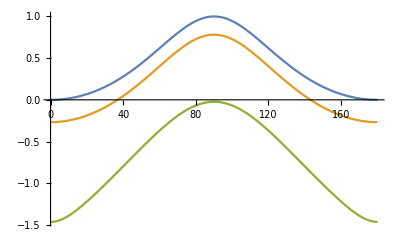

```mathematica
Plot[Evaluate[{dN[π/2,ϕ×π/180,1.064,293],dN[π/5,ϕ×π/180,1.064,293],dN[π/6,ϕ×π/180,1.064,293]}], {ϕ,0,180}]
```

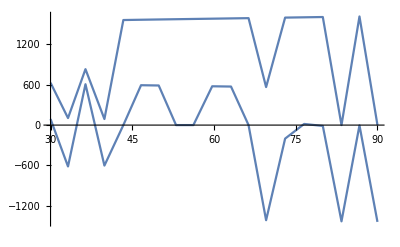

```mathematica
Off[FindRoot::lstol]
Plot[N[180/π Evaluate[{Φssf[θ,1.064,293][[1]],Φssf[θ,1.064,293][[2]]}]],{θ,30,90},PlotPoints->10,MaxRecursion->1,PlotRange->All]
```